```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Github\circular-waveguide

```mathematica
atom=2;(*num of atoms*)
dim=2^atom;(*dimension in Hilbert space*)
(*ALT:Do[bra=ConstantArray[0,{dim,1}];ket=ConstantArray[0,{1,dim}];bra[[i,1]]=1;ket[[1,j]]=1;xij[i,j]=bra.ket,{i,1,dim},{j,1,dim}];*)
 xij[i_,j_]:=ReplacePart[ConstantArray[0,{dim,dim}],{i,j}->1]
ithzero[digit_,kth_]/;kth≤ digit:=Tuples[ReplacePart[Table[{1,0},{digit}],kth->{0}]];

(*jth=1->ith=1*)
(*n digits, kth=0(left is 1, right is n), meaning n atoms, kth in ground state*)
(*ALT: n=5;
ithzero=Compile[{{k,_Integer}},nul={};Do[nul=Append[nul,i*Boole[IntegerDigits[i,2,n][[k]]==0]],{i,0,2^n-1}],nul=Union@nul];*)
(*ALT: For[i=1,i≤ atom,i++,σ[i,1]=Sum[xij[2^atom+1-(x+2^(atom-i)+1),2^atom+1-(x+1)]*Boole[MemberQ[ithzero[atom,i],IntegerDigits[x,2,atom]]],{x,0,2^atom-1}]];*)
Do[σ[i,1]=Sum[xij[2^atom+1-(x+2^(atom-i)+1),2^atom+1-(x+1)]Boole[MemberQ[ithzero[atom,i],IntegerDigits[x,2,atom]]],{x,0,2^atom-1}],{i,1,atom}];
Do[σ[i,0]=Transpose[σ[i,1]],{i,1,atom}];
(*mapping: eeee->1111->2^4-1, i is the ith from the left*)
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
cij[t_]:=Table[c[i,j][t],{i,dim},{j,dim}];
slnc=Flatten[Table[c[i,j][t],{i,dim},{j,dim}]];
init=DiagonalMatrix[Append[ConstantArray[0,dim-1],1]];
λ0=1;k0=2Pi/λ0;
rr=0.5;
sh=Sinh[rr];
ch=Cosh[rr];
ΩR=0.0;
θ=0Pi/2;
r[5]=1 λ0;
r[4]=0.5λ0;
r[3]=0.5λ0;
r[2]=0.5λ0;
r[1]=-0λ0;
Λ[i_,j_]:=(*Λ[i,j]=*)0.5Sin[k0 Abs[r[i]-r[j]] ];
γ[i_,j_]:=(*γ[i,j]=*)Cos[k0 Abs[r[j]-r[i]] ];
γp[i_,j_]:=(*γp[i,j]=Cos[k0(r[i]+r[j])]*)Cos[k0(r[i])]Cos[k0 r[j]];
(*Λ[i_,j_]:=Λ[i,j]=0.5Sin[k0 Abs[r[i]-r[j]] ]KroneckerDelta[i,j];
γ[i_,j_]:=γ[i,j]=Cos[k0 Abs[r[j]-r[i]] ]KroneckerDelta[i,j];
γp[i_,j_]:=γp[i,j]=Cos[k0(r[i]+r[j])]KroneckerDelta[i,j];*)
V=0.5ΩR Sum[Exp[-I θ]Exp[-I k0 r[i]]σ[i,0]+Exp[I θ]Exp[I k0 r[i]]σ[i,1],{i,1,atom}];
SQ=-0.5sh ch Sum[γp[i,j](ρ[t].σ[i,α].σ[j,α]+σ[i,α].σ[j,α].ρ[t]-2σ[j,α].ρ[t].σ[i,α]),{i,1,atom},{j,1,atom},{α,0,1}]-0.5(sh^2+1)Sum[γ[i,j](ρ[t].σ[i,1].σ[j,0]+σ[i,1].σ[j,0].ρ[t]-2σ[j,0].ρ[t].σ[i,1]),{i,1,atom},{j,1,atom}]-0.5 sh^2Sum[γ[i,j](ρ[t].σ[i,0].σ[j,1]+σ[i,0].σ[j,1].ρ[t]-2σ[j,1].ρ[t].σ[i,0]),{i,1,atom},{j,1,atom}]-I Sum[Λ[i,j](σ[i,1].σ[j,0].ρ[t]-ρ[t].σ[i,1].σ[j,0]),{i,1,atom},{j,1,atom}];
SQc=-0.5sh ch Sum[γp[i,j]( cij[t].σ[i,α].σ[j,α]+σ[i,α].σ[j,α]. cij[t]-2σ[j,α]. cij[t].σ[i,α]),{i,1,atom},{j,1,atom},{α,0,1}]-0.5(sh^2+1)Sum[γ[i,j]( cij[t].σ[i,1].σ[j,0]+σ[i,1].σ[j,0]. cij[t]-2σ[j,0]. cij[t].σ[i,1]),{i,1,atom},{j,1,atom}]-0.5 sh^2Sum[γ[i,j]( cij[t].σ[i,0].σ[j,1]+σ[i,0].σ[j,1]. cij[t]-2σ[j,1]. cij[t].σ[i,0]),{i,1,atom},{j,1,atom}]-I Sum[Λ[i,j](σ[i,1].σ[j,0]. cij[t]- cij[t].σ[i,1].σ[j,0]),{i,1,atom},{j,1,atom}];
DR=-I (V.ρ[t]-ρ[t].V);
DRc=-I (V.cij[t]-cij[t].V);
solsq=NDSolve[{ρ'[t]==SQ+DR,ρ[0]==init},slnn,{t,0,1000}];
initc=Sum[σ[i,0],{i,1,atom}].(ρ[t]/.solsq/.t->500)[[1]];
solc=NDSolve[{cij'[t]==SQc+DRc,cij[0]==initc},slnc,{t,0,1000}];
```

```mathematica
(*steady state*)
γ[1,2]=γ[2,1]=Cos[r1-r2];
γp[2,1]=γp[1,2]=Cos[r1]Cos[r2];
γp[1,1]=Cos[r1]Cos[r1];γp[2,2]=Cos[r2]Cos[r2];
m=√(n(n+1));
Solve[{-2(n+1)ρee+n (1+γ[1,2])(ρpp)+n (1-γ[1,2])ρmm+γp[1,2]m ρu==0,
-(2n+1)(1+γ[1,2])ρpp+(n+1) (1+γ[1,2])(ρee)+n (1+γ[1,2])(ρgg)-(γp[1,2]+γp[1,1]/2+γp[2,2]/2)m ρu==0,-(2n+1)(1-γ[1,2])ρmm+(n +1)(1-γ[1,2])(ρee)+n (1-γ[1,2])ρgg-(γp[1,2]-γp[1,1]/2-γp[2,2]/2)m ρu==0,-(2n+1) ρu-2m(γp[1,2]+γp[1,1]/2+γp[2,2]/2)ρpp-2m(γp[1,2]-γp[1,1]/2-γp[2,2]/2)ρmm+2m γp[1,2](ρgg+ρee)==0,ρee+ρpp+ρmm+ρgg==1},{ρee,ρpp,ρmm,ρu,ρgg}]//Simplify
```

{{ρee→(n (-2-10 n-20 n^2-20 n^3+(-2-2 n+8 n^2+8 n^3) Cos[2 r1]-(1+n) Cos[2 (r1-r2)]-2 Cos[2 r2]-2 n Cos[2 r2]+8 n^2 Cos[2 r2]+8 n^3 Cos[2 r2]-Cos[2 (r1+r2)]-n Cos[2 (r1+r2)]+4 n^2 Cos[2 (r1+r2)]+4 n^3 Cos[2 (r1+r2)]))/(4 (-2-14 n-34 n^2-40 n^3-20 n^4+n (1+9 n+16 n^2+8 n^3) Cos[2 r1]-n (1+n) Cos[2 (r1-r2)]+n Cos[2 r2]+9 n^2 Cos[2 r2]+16 n^3 Cos[2 r2]+8 n^4 Cos[2 r2]+n Cos[2 (r1+r2)]+5 n^2 Cos[2 (r1+r2)]+8 n^3 Cos[2 (r1+r2)]+4 n^4 Cos[2 (r1+r2)])),ρpp→(n (1+n) (-8-20 n-20 n^2+8 n (1+n) Cos[2 r1]+4 Cos[r1-r2]-Cos[2 (r1-r2)]+8 n Cos[2 r2]+8 n^2 Cos[2 r2]+4 Cos[r1+r2]+Cos[2 (r1+r2)]+4 n Cos[2 (r1+r2)]+4 n^2 Cos[2 (r1+r2)]))/(4 (-2-14 n-34 n^2-40 n^3-20 n^4+n (1+9 n+16 n^2+8 n^3) Cos[2 r1]-n (1+n) Cos[2 (r1-r2)]+n Cos[2 r2]+9 n^2 Cos[2 r2]+16 n^3 Cos[2 r2]+8 n^4 Cos[2 r2]+n Cos[2 (r1+r2)]+5 n^2 Cos[2 (r1+r2)]+8 n^3 Cos[2 (r1+r2)]+4 n^4 Cos[2 (r1+r2)])),ρmm→(n (1+n) (-8-20 n-20 n^2+8 n (1+n) Cos[2 r1]-4 Cos[r1-r2]-Cos[2 (r1-r2)]+8 n Cos[2 r2]+8 n^2 Cos[2 r2]-4 Cos[r1+r2]+Cos[2 (r1+r2)]+4 n Cos[2 (r1+r2)]+4 n^2 Cos[2 (r1+r2)]))/(4 (-2-14 n-34 n^2-40 n^3-20 n^4+n (1+9 n+16 n^2+8 n^3) Cos[2 r1]-n (1+n) Cos[2 (r1-r2)]+n Cos[2 r2]+9 n^2 Cos[2 r2]+16 n^3 Cos[2 r2]+8 n^4 Cos[2 r2]+n Cos[2 (r1+r2)]+5 n^2 Cos[2 (r1+r2)]+8 n^3 Cos[2 (r1+r2)]+4 n^4 Cos[2 (r1+r2)])),ρu→-((4 n (1+3 n+2 n^2) Cos[r1] Cos[r2])/(√(n (1+n)) (-2-14 n-34 n^2-40 n^3-20 n^4+n (1+9 n+16 n^2+8 n^3) Cos[2 r1]-n (1+n) Cos[2 (r1-r2)]+n Cos[2 r2]+9 n^2 Cos[2 r2]+16 n^3 Cos[2 r2]+8 n^4 Cos[2 r2]+n Cos[2 (r1+r2)]+5 n^2 Cos[2 (r1+r2)]+8 n^3 Cos[2 (r1+r2)]+4 n^4 Cos[2 (r1+r2)]))),ρgg→((1+n) (-8-30 n-40 n^2-20 n^3+2 n (3+8 n+4 n^2) Cos[2 r1]-n Cos[2 (r1-r2)]+6 n Cos[2 r2]+16 n^2 Cos[2 r2]+8 n^3 Cos[2 r2]+3 n Cos[2 (r1+r2)]+8 n^2 Cos[2 (r1+r2)]+4 n^3 Cos[2 (r1+r2)]))/(4 (-2-14 n-34 n^2-40 n^3-20 n^4+n (1+9 n+16 n^2+8 n^3) Cos[2 r1]-n (1+n) Cos[2 (r1-r2)]+n Cos[2 r2]+9 n^2 Cos[2 r2]+16 n^3 Cos[2 r2]+8 n^4 Cos[2 r2]+n Cos[2 (r1+r2)]+5 n^2 Cos[2 (r1+r2)]+8 n^3 Cos[2 (r1+r2)]+4 n^4 Cos[2 (r1+r2)]))}}

```mathematica
ρ[t]/.solsq/.t->300//MatrixForm
```

((0.175973+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.380797+0. ⅈ) | (0.+0. ⅈ
2.24304×10^-15+0. ⅈ
2.25916×10^-15+0. ⅈ
0.+0. ⅈ) | (0.+0. ⅈ
2.26025×10^-15+0. ⅈ
2.23484×10^-15+0. ⅈ
0.+0. ⅈ) | (0.380797+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.824027+0. ⅈ))

-Graphics3D-

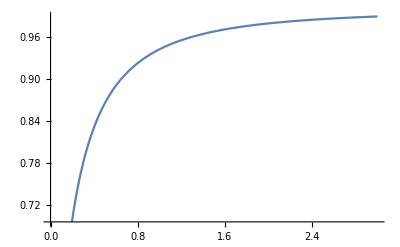

```mathematica
Show[ListPlot3D[Table[Abs[(2 n (1+3 n+2 n^2) Cos[2Pi dr])/(√(n (1+n)) (1+6 n+6 n^2+2 n (1+n) Cos[2 (2Pi dr)]))]-(4 n (1+n) Sin[(2Pi dr)/2]^4)/((1+2 n)^2+4 n (1+n) Cos[2Pi dr]^2)-(4 n (1+n) Cos[(2Pi dr)/2]^4)/((1+2 n)^2+4 n (1+n) Cos[2Pi dr]^2),{dr,0.001,1.001,0.05},{n,0.02,3,0.02}],DataRange->{{0,3},{0,1}},PlotRange->{-0.,1},AxesStyle->Directive[Black,FontSize->18]],Graphics3D[Text[Style["N",Large],Scaled[{0.5,1.1,1.1}]]],Graphics3D[Text[Style["Δr/λ_(0  z)",Large],Scaled[{-0.25,0.5,0.2}]]],Graphics3D[Text[Style["C",Large],Scaled[{-.1,1.1,1.1}]]]]
Plot[Abs[(√(n (1+n)) (n (6+4 n)-2 (2+3 n+2 n^2)))/(2+7 n+12 n^2+8 n^3+4 n (1+n)-n (7+16 n+8 n^2))],{n,0,3},PlotLegends->"Concurrence"]
```

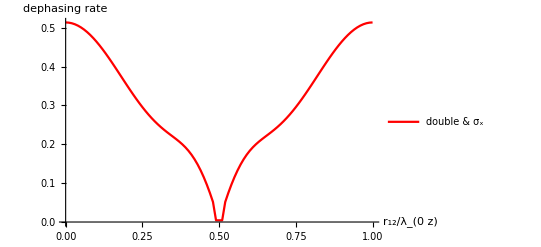

```mathematica
initx=1/4ConstantArray[1,{4,4}];
solsqx=NDSolve[{ρ'[t]==-0.5sh ch Sum[γp[i,j](ρ[t].σ[i,α].σ[j,α]+σ[i,α].σ[j,α].ρ[t]-2σ[j,α].ρ[t].σ[i,α]),{i,1,atom},{j,1,atom},{α,0,1}]-0.5(sh^2+1)Sum[γ[i,j](ρ[t].σ[i,1].σ[j,0]+σ[i,1].σ[j,0].ρ[t]-2σ[j,0].ρ[t].σ[i,1]),{i,1,atom},{j,1,atom}]-0.5 sh^2Sum[γ[i,j](ρ[t].σ[i,0].σ[j,1]+σ[i,0].σ[j,1].ρ[t]-2σ[j,1].ρ[t].σ[i,0]),{i,1,atom},{j,1,atom}]-I Sum[Λ[i,j](σ[i,1].σ[j,0].ρ[t]-ρ[t].σ[i,1].σ[j,0]),{i,1,atom},{j,1,atom}],ρ[0]==initx},slnn,{t,0,1000}];
dphx=ListLinePlot[Table[{n,
δ=10^-7;di=n λ0;
Λ[1,1]=Λ[2,2]=0;
Λ[1,2]=Λ[2,1]=0.5Sin[k0 Abs[di] ];
γ[1,1]=γ[2,2]=γp[1,1]=γp[2,2]=1;
γ[1,2]=γ[2,1]=γp[1,2]=γp[2,1]=Cos[k0 di ];
solsqx=NDSolve[{ρ'[t]==-0.5sh ch Sum[γp[i,j](ρ[t].σ[i,α].σ[j,α]+σ[i,α].σ[j,α].ρ[t]-2σ[j,α].ρ[t].σ[i,α]),{i,1,atom},{j,1,atom},{α,0,1}]-0.5(sh^2+1)Sum[γ[i,j](ρ[t].σ[i,1].σ[j,0]+σ[i,1].σ[j,0].ρ[t]-2σ[j,0].ρ[t].σ[i,1]),{i,1,atom},{j,1,atom}]-0.5 sh^2Sum[γ[i,j](ρ[t].σ[i,0].σ[j,1]+σ[i,0].σ[j,1].ρ[t]-2σ[j,1].ρ[t].σ[i,0]),{i,1,atom},{j,1,atom}]-I Sum[Λ[i,j](σ[i,1].σ[j,0].ρ[t]-ρ[t].σ[i,1].σ[j,0]),{i,1,atom},{j,1,atom}],ρ[0]==initx,WhenEvent[Re[Evaluate[a[1,3][t]/.solsqx]+Evaluate[a[2,4][t]/.solsqx]+Evaluate[a[3,1][t]/.solsqx]+Evaluate[a[4,2][t]/.solsqx]][[1]]==1/E,dx=1/t]},slnn,{t,0,1000},MaxSteps->50000];dx},{n,0.0,1,0.01}],AxesLabel->{"r_12/λ_(0  z)","dephasing rate"},PlotStyle->Red,PlotLegends->LineLegend[{"double & σ_x"}]]
```

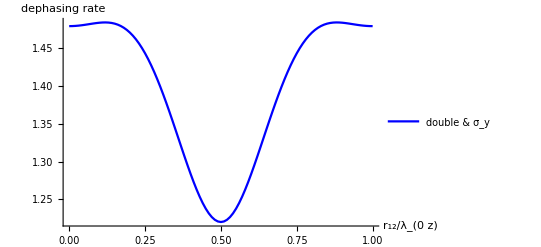

```mathematica
inity=({{1, -I, -I, -1}, {I, 1, 1, -I}, {I, 1, 1, -I}, {-1, I, I, 1}})/4;
solsqy=NDSolve[{ρ'[t]==-0.5sh ch Sum[γp[i,j](ρ[t].σ[i,α].σ[j,α]+σ[i,α].σ[j,α].ρ[t]-2σ[j,α].ρ[t].σ[i,α]),{i,1,atom},{j,1,atom},{α,0,1}]-0.5(sh^2+1)Sum[γ[i,j](ρ[t].σ[i,1].σ[j,0]+σ[i,1].σ[j,0].ρ[t]-2σ[j,0].ρ[t].σ[i,1]),{i,1,atom},{j,1,atom}]-0.5 sh^2Sum[γ[i,j](ρ[t].σ[i,0].σ[j,1]+σ[i,0].σ[j,1].ρ[t]-2σ[j,1].ρ[t].σ[i,0]),{i,1,atom},{j,1,atom}]-I Sum[Λ[i,j](σ[i,1].σ[j,0].ρ[t]-ρ[t].σ[i,1].σ[j,0]),{i,1,atom},{j,1,atom}],ρ[0]==inity},slnn,{t,0,1000}];
dphy=ListLinePlot[Table[{n,
δ=10^-7;di=n λ0;
Λ[1,1]=Λ[2,2]=0;
Λ[1,2]=Λ[2,1]=0.5Sin[k0 Abs[di] ];
γ[1,1]=γ[2,2]=γp[1,1]=γp[2,2]=1;
γ[1,2]=γ[2,1]=γp[1,2]=γp[2,1]=Cos[k0 di ];
solsqx=NDSolve[{ρ'[t]==-0.5sh ch Sum[γp[i,j](ρ[t].σ[i,α].σ[j,α]+σ[i,α].σ[j,α].ρ[t]-2σ[j,α].ρ[t].σ[i,α]),{i,1,atom},{j,1,atom},{α,0,1}]-0.5(sh^2+1)Sum[γ[i,j](ρ[t].σ[i,1].σ[j,0]+σ[i,1].σ[j,0].ρ[t]-2σ[j,0].ρ[t].σ[i,1]),{i,1,atom},{j,1,atom}]-0.5 sh^2Sum[γ[i,j](ρ[t].σ[i,0].σ[j,1]+σ[i,0].σ[j,1].ρ[t]-2σ[j,1].ρ[t].σ[i,0]),{i,1,atom},{j,1,atom}]-I Sum[Λ[i,j](σ[i,1].σ[j,0].ρ[t]-ρ[t].σ[i,1].σ[j,0]),{i,1,atom},{j,1,atom}],ρ[0]==inity,WhenEvent[Im[-Evaluate[a[1,3][t]/.solsqy]-Evaluate[a[2,4][t]/.solsqy]+Evaluate[a[3,1][t]/.solsqy]+Evaluate[a[4,2][t]/.solsqy]][[1]]==1/E,dx=1/t]},slnn,{t,0,1000},MaxSteps->50000];dx},{n,0.0,1,0.01}],AxesLabel->{"r_12/λ_(0  z)","dephasing rate"},PlotStyle->Blue,PlotLegends->LineLegend[{"double & σ_y"}]]
```

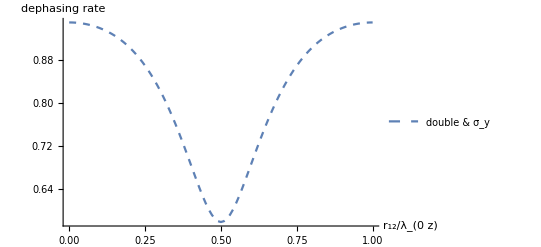

```mathematica
inity=({{1, -I, -I, -1}, {I, 1, 1, -I}, {I, 1, 1, -I}, {-1, I, I, 1}})/4;
solsqy=NDSolve[{ρ'[t]==-0.5sh ch Sum[γp[i,j](ρ[t].σ[i,α].σ[j,α]+σ[i,α].σ[j,α].ρ[t]-2σ[j,α].ρ[t].σ[i,α]),{i,1,atom},{j,1,atom},{α,0,1}]-0.5(sh^2+1)Sum[γ[i,j](ρ[t].σ[i,1].σ[j,0]+σ[i,1].σ[j,0].ρ[t]-2σ[j,0].ρ[t].σ[i,1]),{i,1,atom},{j,1,atom}]-0.5 sh^2Sum[γ[i,j](ρ[t].σ[i,0].σ[j,1]+σ[i,0].σ[j,1].ρ[t]-2σ[j,1].ρ[t].σ[i,0]),{i,1,atom},{j,1,atom}]-I Sum[Λ[i,j](σ[i,1].σ[j,0].ρ[t]-ρ[t].σ[i,1].σ[j,0]),{i,1,atom},{j,1,atom}],ρ[0]==inity},slnn,{t,0,1000}];
dphy=ListLinePlot[Table[{n,
δ=10^-7;di=n λ0;
Λ[1,1]=Λ[2,2]=0;
Λ[1,2]=Λ[2,1]=0.5Sin[k0 Abs[di] ];
γ[1,1]=γ[2,2]=γp[1,1]=γp[2,2]=1;
γ[1,2]=γ[2,1]=γp[1,2]=γp[2,1]=Cos[k0 di ];
solsqx=NDSolve[{ρ'[t]==-0.5(sh^2+1)Sum[γ[i,j](ρ[t].σ[i,1].σ[j,0]+σ[i,1].σ[j,0].ρ[t]-2σ[j,0].ρ[t].σ[i,1]),{i,1,atom},{j,1,atom}]-0.5 sh^2Sum[γ[i,j](ρ[t].σ[i,0].σ[j,1]+σ[i,0].σ[j,1].ρ[t]-2σ[j,1].ρ[t].σ[i,0]),{i,1,atom},{j,1,atom}]-I Sum[Λ[i,j](σ[i,1].σ[j,0].ρ[t]-ρ[t].σ[i,1].σ[j,0]),{i,1,atom},{j,1,atom}],ρ[0]==inity,WhenEvent[Im[-Evaluate[a[1,3][t]/.solsqy]-Evaluate[a[2,4][t]/.solsqy]+Evaluate[a[3,1][t]/.solsqy]+Evaluate[a[4,2][t]/.solsqy]][[1]]==1/E,dx=1/t]},slnn,{t,0,1000},MaxSteps->50000];dx},{n,0.0,1,0.01}],AxesLabel->{"r_12/λ_(0  z)","dephasing rate"},PlotStyle->Dashed,PlotLegends->LineLegend[{"double & σ_y"}]]
```

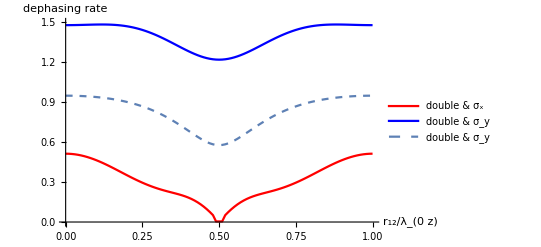

```mathematica
Show[{Out[410],Out[419],Out[422]},PlotRange->{0,1.5}]
```

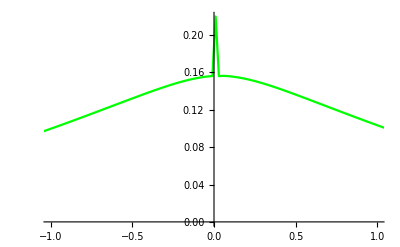

```mathematica
ss=Tr[((cij[t]/.solc)[[1]].Sum[σ[i,1],{i,1,atom}])]/.t->500;
dt=0.01;
spec=Flatten[Re[InverseFourier[Table[Tr[((cij[t]/.solc)[[1]].Sum[σ[i,1],{i,1,atom}])]-ss,{t,0,100Pi,dt}]]]];
p=IntegerPart[100Pi/dt/2];
specc=ConstantArray[0,2p];
spec=spec;
specc[[1;;p]]=spec[[p+1;;2p]];
specc[[p+1;;2p]]=spec[[1;;p]];
aaa=ListLinePlot[specc,DataRange->{-Pi 1/dt,Pi 1/dt},PlotRange->{{-1,1},Full},PlotLegends->"vac",PlotStyle->Green]
```

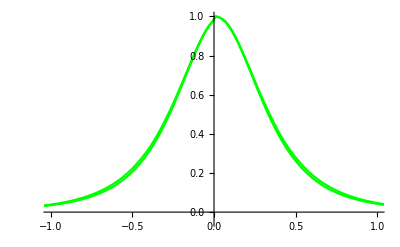

```mathematica
Show[Out[89],Out[129]]
```

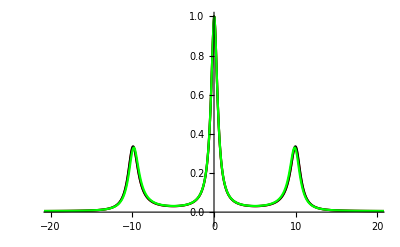

```mathematica
Show[Out[185],Out[225],Out[266]]
```

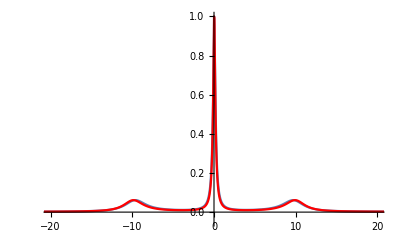

```mathematica
Show[Out[90],Out[144]]
```

```mathematica
Quit[]
```

```mathematica
atom=2;(*num of atoms*)
dim=2^atom;(*dimension in Hilbert space*)

 xij[i_,j_]:=ReplacePart[ConstantArray[0,{dim,dim}],{i,j}->1]
ithzero[digit_,kth_]/;kth≤ digit:=Tuples[ReplacePart[Table[{1,0},{digit}],kth->{0}]];

Do[σ[i,1]=Sum[xij[2^atom+1-(x+2^(atom-i)+1),2^atom+1-(x+1)]Boole[MemberQ[ithzero[atom,i],IntegerDigits[x,2,atom]]],{x,0,2^atom-1}],{i,1,atom}];
Do[σ[i,0]=Transpose[σ[i,1]],{i,1,atom}];
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
cij[t_]:=Table[c[i,j][t],{i,dim},{j,dim}];
slnc=Flatten[Table[c[i,j][t],{i,dim},{j,dim}]];
init=ConstantArray[1/2^atom,{dim,dim}];

λ0=1;k0=2Pi/λ0;
rr=0.5;
sh=Sinh[rr];
ch=Cosh[rr];
Table[{n,d=n λ0;
Do[r[i]=(i-1) λ0+d,{i,1,atom}];
Λ[i_,j_]:=(*Λ[i,j]=*)0.5Sin[k0 Abs[r[i]-r[j]] ];
γ[i_,j_]:=(*γ[i,j]=*)Cos[k0 Abs[r[j]-r[i]] ];
γp[i_,j_]:=(*γp[i,j]=*)Cos[k0(r[i]+r[j])];

SQ=-0.5sh ch Sum[γp[i,j](ρ[t].σ[i,α].σ[j,α]+σ[i,α].σ[j,α].ρ[t]-2σ[j,α].ρ[t].σ[i,α]),{i,1,atom},{j,1,atom},{α,0,1}]-0.5(sh^2+1)Sum[γ[i,j](ρ[t].σ[i,1].σ[j,0]+σ[i,1].σ[j,0].ρ[t]-2σ[j,0].ρ[t].σ[i,1]),{i,1,atom},{j,1,atom}]-0.5 sh^2Sum[γ[i,j](ρ[t].σ[i,0].σ[j,1]+σ[i,0].σ[j,1].ρ[t]-2σ[j,1].ρ[t].σ[i,0]),{i,1,atom},{j,1,atom}]-I Sum[Λ[i,j](σ[i,1].σ[j,0].ρ[t]-ρ[t].σ[i,1].σ[j,0]),{i,1,atom},{j,1,atom}];
solsq=NDSolve[{ρ'[t]==SQ,ρ[0]==init},slnn,{t,0,1000},MaxSteps->50000];
solsq=NDSolve[{ρ'[t]==SQ,ρ[0]==init,WhenEvent[Re[(a[1,3][t]+a[2,4][t]+a[3,1][t]+a[4,2][t])/.solsq][[1]]==1/E,dx=1/t]},slnn,{t,0,1000},MaxSteps->50000];dx},{n,0.0,1,0.02}]
```

{{0.,0.513497},{0.02,0.523746},{0.04,0.555851},{0.06,0.612392},{0.08,0.694138},{0.1,0.798176},{0.12,0.918068},{0.14,1.04513},{0.16,1.16977},{0.18,1.28264},{0.2,1.37536},{0.22,1.44115},{0.24,1.47527},{0.26,1.47527},{0.28,1.44115},{0.3,1.37536},{0.32,1.28264},{0.34,1.16977},{0.36,1.04513},{0.38,0.918068},{0.4,0.798176},{0.42,0.694138},{0.44,0.612392},{0.46,0.555851},{0.48,0.523746},{0.5,0.513497},{0.52,0.523746},{0.54,0.555851},{0.56,0.612392},{0.58,0.694138},{0.6,0.798176},{0.62,0.918068},{0.64,1.04513},{0.66,1.16977},{0.68,1.28264},{0.7,1.37536},{0.72,1.44115},{0.74,1.47527},{0.76,1.47527},{0.78,1.44115},{0.8,1.37536},{0.82,1.28264},{0.84,1.16977},{0.86,1.04513},{0.88,0.918068},{0.9,0.798176},{0.92,0.694138},{0.94,0.612392},{0.96,0.555851},{0.98,0.523746},{1.,0.513497}}